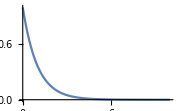

```mathematica
Plot[Exp[-x],{x,0.000,10^1},PlotRange->Full]
```

```mathematica
f[x_]:=1-Exp[-x]
```

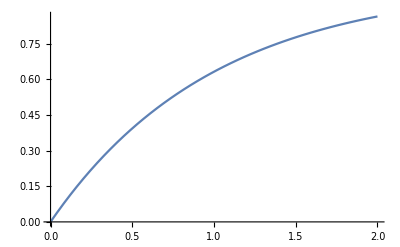

```mathematica
Plot[f[x],{x,0.0,2},PlotRange->Full]
```

```mathematica
f[4]//N
f[2]//N
f[1]//N
f[0.7]//N
f[0.07]//N
```

0.981684

0.864665

0.632121

0.503415

0.0676062

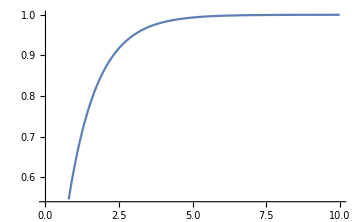
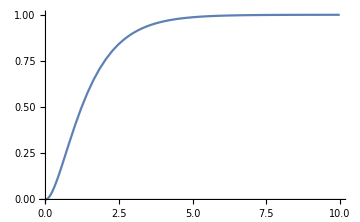

```mathematica
{Plot[f[y]           ,{y,0,10},ImageSize->Medium],
Plot[f[y] f[y],{y,0,10},ImageSize->Medium]}
```

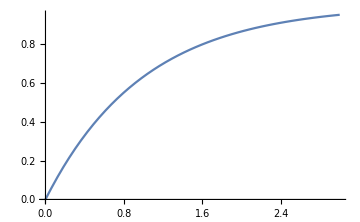
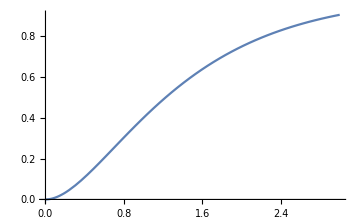

```mathematica
{Plot[f[y]           ,{y,0,3},ImageSize->Medium],
Plot[f[y] f[y],{y,0,3},ImageSize->Medium]}
```

```mathematica
Quit
```

desired object frame velocity :
fast : 3 sec of observation and crossing the screen in Width direction
slow: 10 sec of observation in image.
assuming crossing the image from side to side in that period:
T=3~10
df/dx estimated is W/(T FPS) ~ i.e 320/(3 30)=

wanting B_p^m levels as  
0.7
0.5
0.3
what are the λ^m required ?

```mathematica
f[1.2]//N
f[0.4]//N
```

0.698806

0.32968

```mathematica
Tmin=3
Tmax=10

Tmin=10
Tmax=30

W=320
FPS =30
velMax=W/(T FPS)/.T->Tmin//N
velMin=W/(T FPS)/.T->Tmax//N
```

3

10

10

30

320

30

1.06667

0.355556

```mathematica
fGrad = velMax;
λ^m=1.2/fGrad
fGrad = velMin;
λ^m=0.4/fGrad
```

Set::write: Tag Power in λ^m is Protected.

1.125

Set::write: Tag Power in λ^m is Protected.

1.125